en = energy, enc = energy at the Compton edge

```mathematica
gaussian[en_]=PDF[NormalDistribution[0,σ],en]
```

(ⅇ^(-en^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
modelr[en_] = Piecewise[{{a1*en^2+b1*en+c1, en<=enc}, {0, en>enc}}];
```

max of modelr is a*enc^2*b*enc+c at enc

```mathematica
modelr2[en_] = (a1*en^2+b1*en+c1)*(-UnitStep[en-enc]+1);
```

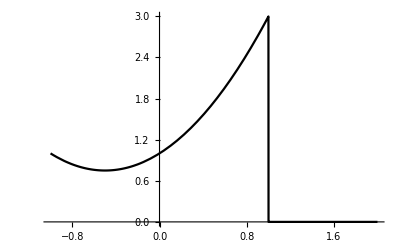

```mathematica
modelr2plt=Plot[modelr2[en]/.{a1->1,b1->1,c1->1,enc->1},{en,-1,2},PlotStyle->Black]
```

```mathematica
cmodelr[en_]=Convolve[modelr[en],gaussian[en],en,en2];
```

```mathematica
simplcmodelr=Simplify[cmodelr[en],a1>0&&b1>0&&c1>0&&σ>0&&en2>0&&enc>0]
```

1/2 (c1+b1 (en2-ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) σ)+a1 (en2^2-ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2+enc) √(2/π) σ+σ^2)-(c1+b1 en2+a1 (en2^2+σ^2)) Erf[(en2-enc)/(√2 σ)])

Value at theoretical compton edge

```mathematica
Expand[simplcmodelr/.{en2->enc}]
```

c1/2+(b1 enc)/2+(a1 enc^2)/2-a1 enc √(2/π) σ-(b1 σ)/(√(2 π))+(a1 σ^2)/2

```mathematica
cmodelr2 [en_] =Convolve[modelr2[en],gaussian[en],en,en2];
```

```mathematica
simplcmodelr2 =Simplify[cmodelr2[en],a1>0&&b1>0&&c1>0&&σ>0&&en2>0&&enc>0]
```

1/2 (c1+b1 (en2-ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) σ)+a1 (en2^2-ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2+enc) √(2/π) σ+σ^2)-c1 Erf[(en2-enc)/(√2 σ)]-(b1 en2+a1 (en2^2+σ^2)) Erf[(en2-enc)/(√2 σ)])

```mathematica
Expand[simplcmodelr2/.{en2->enc}]
```

c1/2+(b1 enc)/2+(a1 enc^2)/2-a1 enc √(2/π) σ-(b1 σ)/(√(2 π))+(a1 σ^2)/2

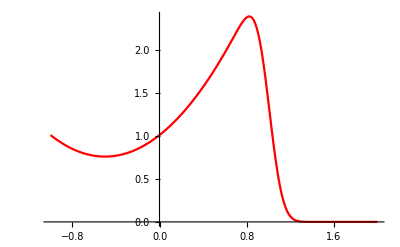

```mathematica
cmodelr2plt = Plot[cmodelr2[en]/.{a1->1,b1->1,c1->1,enc->1,σ->0.1},{en2,-1,2},PlotStyle->Red]
```

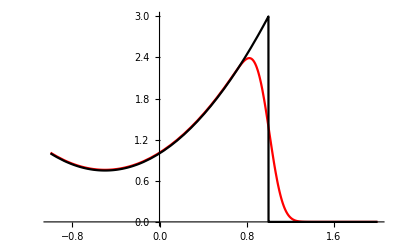

```mathematica
Show[{cmodelr2plt,modelr2plt},PlotRange->Full]
```

Doing it straight from the Iranian paper

```mathematica
erfc[en_] = 1-2/(√π)*∫_0^en E^(-x^2)ⅆx
```

1-Erf[en]

```mathematica
erfc[0]
```

1

```mathematica
alpha1[en_] = 1/2(a1*(en^2+σ^2)+b1*en+c1)
```

1/2 (c1+b1 en+a1 (en^2+σ^2))

```mathematica
beta1[en_] = -σ/(√(2π))a1(en+enc)+b1
```

b1-(a1 (en+enc) σ)/(√(2 π))

```mathematica
convolvedR[en_] = alpha1[en]*erfc[Abs[(en-enc)/(√2 σ)]]-beta1[en]*Exp[Abs[-(en-enc)^2/(2 σ^2) ]]
```

-ⅇ^(1/2 Abs[(en-enc)^2/σ^2]) (b1-(a1 (en+enc) σ)/(√(2 π)))+1/2 (c1+b1 en+a1 (en^2+σ^2)) (1-Erf[Abs[(en-enc)/σ]/(√2)])

```mathematica
Expand[convolvedR[en]/.{en->enc}]
```

-b1+c1/2+(b1 enc)/2+(a1 enc^2)/2+a1 enc √(2/π) σ+(a1 σ^2)/2

```mathematica
Expand[simplcmodelr2/.{en2->enc}]
```

c1/2+(b1 enc)/2+(a1 enc^2)/2-a1 enc √(2/π) σ-(b1 σ)/(√(2 π))+(a1 σ^2)/2

```mathematica
modelrmax = a1*enc^2+b1*enc+c1
```

c1+b1 enc+a1 enc^2

Convolution components in Iranian paper matches Mathematica convolution results

Derivatives of models

```mathematica
dsimplcmodelr =D[simplcmodelr,en2]
```

1/2 (b1 (1+(ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2-enc) √(2/π))/σ)+a1 (2 en2+(ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2-enc) (en2+enc) √(2/π))/σ-ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) σ)-(ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) (c1+b1 en2+a1 (en2^2+σ^2)))/σ-(b1+2 a1 en2) Erf[(en2-enc)/(√2 σ)])

```mathematica
Expand[dsimplcmodelr /.{en2->enc}]
```

b1/2+a1 enc-c1/(√(2 π) σ)-(b1 enc)/(√(2 π) σ)-(a1 enc^2)/(√(2 π) σ)-a1 √(2/π) σ

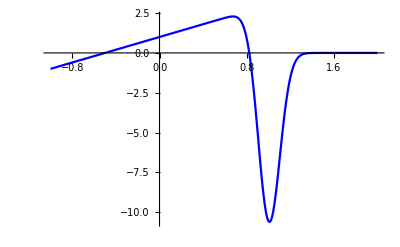

```mathematica
dsimplcmodelrplt = Plot[dsimplcmodelr/.{a1->1,b1->1,c1->1,enc->1,σ->0.1},{en2,-1,2},PlotStyle->Blue,PlotRange->Full]
```

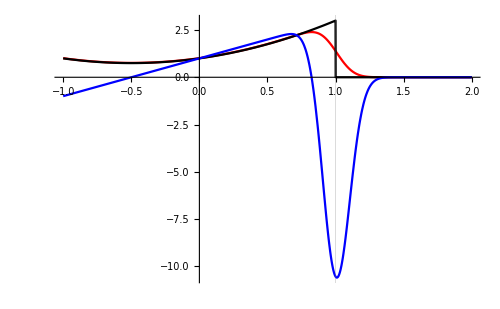

```mathematica
Show[{cmodelr2plt,modelr2plt,dsimplcmodelrplt},PlotRange->Full,GridLines->{{{1.0,Thick}},{}},ImageSize->500]
```

Adjusting sigma of convolved result

```mathematica
modelr2plt1=Plot[modelr2[en]/.{a1->1,b1->1,c1->1,enc->2},{en,0,3},PlotStyle->Black];
cmodelr2plts1 = Plot[cmodelr2[en]/.{a1->1,b1->1,c1->1,enc->2,σ->0.05},{en2,0,3},PlotStyle->Red,PlotLabel->"σ=0.05"];
cmodelr2plts2 = Plot[cmodelr2[en]/.{a1->1,b1->1,c1->1,enc->2,σ->0.075},{en2,0,3},PlotStyle->Red,PlotLabel->"σ=0.075"];
cmodelr2plts3 = Plot[cmodelr2[en]/.{a1->1,b1->1,c1->1,enc->2,σ->0.1},{en2,0,3},PlotStyle->Red,PlotLabel->"σ=0.1"];
cmodelr2plts4 = Plot[cmodelr2[en]/.{a1->1,b1->1,c1->1,enc->2,σ->0.125},{en2,0,3},PlotStyle->Red,PlotLabel->"σ=0.125"];
```

General::munfl: Exp[-799.951] is too small to represent as a normalized machine number; precision may be lost.

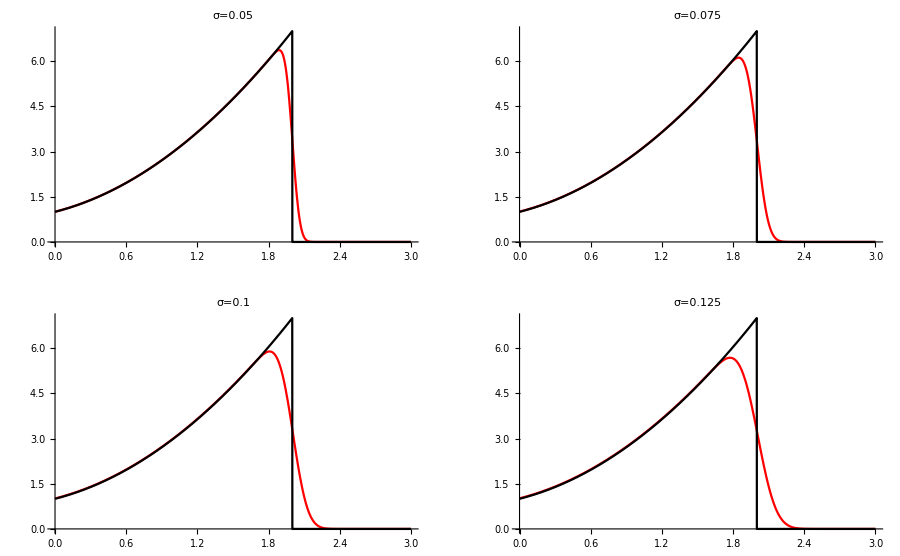

```mathematica
GraphicsGrid[{{Show[{cmodelr2plts1,modelr2plt1},PlotRange->Full],Show[{cmodelr2plts2,modelr2plt1},PlotRange->Full]},{Show[{cmodelr2plts3,modelr2plt1},PlotRange->Full],Show[{cmodelr2plts4,modelr2plt1},PlotRange->Full]}},ImageSize->900]
```

```mathematica
modelr[en]
```

Piecewise[{{c1+b1 en+a1 en^2, en≤enc}, {0, True}}]

```mathematica
simplcmodelr
```

1/2 (c1+b1 (en2-ⅇ^(-(en2-enc)^2/(2 σ^2)) √(2/π) σ)+a1 (en2^2-ⅇ^(-(en2-enc)^2/(2 σ^2)) (en2+enc) √(2/π) σ+σ^2)-(c1+b1 en2+a1 (en2^2+σ^2)) Erf[(en2-enc)/(√2 σ)])